```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichiro/Documents/Univ/SLattice/peak_theory

## Peak Theory

```mathematica
npeak=16;
NL=256;
L=10^-12;(*Mpc*)
kpeak=2π npeak/NL;
```

### Monochromatic

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_,ks_]=ks^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

```mathematica
Cm[nu2_,As_]=2/3(1-(1+xm Sinc'[xm]Sqrt[As]nu2)^2)/.{xm->2.74};
```

```mathematica
dlnMdmu2[nu2_,As_]=2Sqrt[As]Sinc[xm]+γ/(Cm[nu2,As]-Cth)D[Cm[nu2,As], nu2]/.{Cth->0.533,γ->0.36,xm->2.74}//Simplify;
```

```mathematica
nPBHpk[nu2_,ks_,As_]=nnu2PT[nu2,ks]/Abs[dlnMdmu2[nu2,As]];
```

```mathematica
Mpk[nu2_,As_]=xm^2 Exp[2Sqrt[As]Sinc[xm]nu2](Cm[nu2,As]-Cth)^γ/.{Cth->0.533,γ->0.36,xm->2.74};
Mks[ks_]=(NL/L ks/(1.56 10^13))^-2;
```

```mathematica
fPBHpk[nu2_,ks_,As_]=Mks[ks] Mpk[nu2,As] nPBHpk[nu2,ks,As]/(3.95 10^-20);
```

```mathematica
Mkpeak=Mks[kpeak]
```

0.0240796

```mathematica
Azeta=3.625 10^-3;
nu2th=nu2/.FindRoot[Cm[nu2,Azeta]==0.533,{nu2,8}];
fPBHpkList=Table[{Mkpeak Mpk[nu2th+10^dlnnu2,Azeta],fPBHpk[nu2th+10^dlnnu2,kpeak,Azeta]},{dlnnu2,-5,1/2,10^-2}];
```

```mathematica
Mmin=First[fPBHpkList][[1]]
Mmax=Last[fPBHpkList][[1]]
```

0.00102593

0.0943306

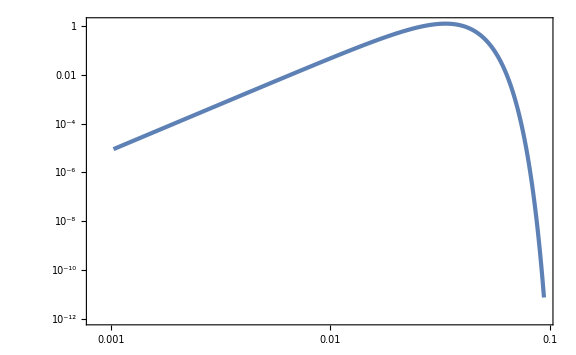

```mathematica
ListLogLogPlot[fPBHpkList]
```

```mathematica
fPBHpkint[M_]=Interpolation[fPBHpkList][M];
NIntegrate[fPBHpkint[M]/M,{M,Mmin,Mmax}]
```

1.00416

```mathematica
Export["data/fPBH_pk_mono.csv",fPBHpkList];
```

### Sharp lognormal

```mathematica
s2s=10^-2;
```

```mathematica
calPz[lnk_,s2_]=Ag/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
σn2[n_,s2_]=Ag E^(2 n^2 s2)ks^(2n);
```

```mathematica
Rn[n_,s2_]=Simplify[Sqrt[3 σn2[n,s2]/σn2[n+1,s2]],{s2>0,n>0,ks>0}]
```

(√3 ⅇ^(-((1+2 n) s2)))/ks

```mathematica
γn[s2_]=Simplify[σn2[n,s2]/Sqrt[σn2[n-1,s2]σn2[n+1,s2]],{ks>0,n>0,s2>0,Ag>0}]
```

ⅇ^(-2 s2)

```mathematica
ψn[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2]Sinc[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnp[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^((2n +1)lnk)calPz[lnk,s2]Sinc'[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnpp[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^((2n +2)lnk)calPz[lnk,s2]Sinc''[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψn[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψnp[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψnpp[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψn[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψnp[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψnpp[x,2,s2s]},{x,10^-2,10,10^-2}];]
```

{42.2028,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=Simplify[(1/(1-γn[s2]^2)(ψ1int[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2int[x])-k3t^2/(γn[s2](1-γn[s2]^2))(γn[s2]^2 ψ1int[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2int[x]))/.{s2->s2s}];
ζp[x_,k3t_]=Simplify[(1/(1-γn[s2]^2)(ψ1pint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2pint[x])-k3t^2/(γn[s2](1-γn[s2]^2))(γn[s2]^2 ψ1pint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2pint[x]))/.{s2->s2s}];
ζpp[x_,k3t_]=Simplify[(1/(1-γn[s2]^2)(ψ1ppint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2ppint[x])-k3t^2/(γn[s2](1-γn[s2]^2))(γn[s2]^2 ψ1ppint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2ppint[x]))/.{s2->s2s}];
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3//Simplify;
```

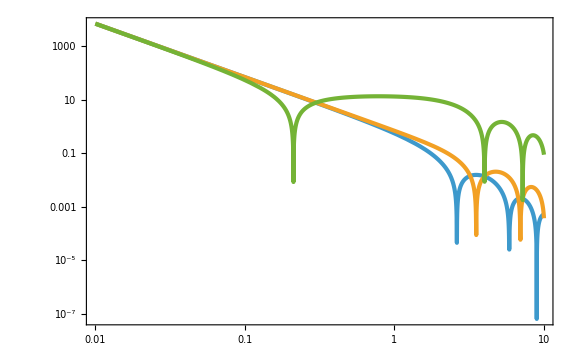

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

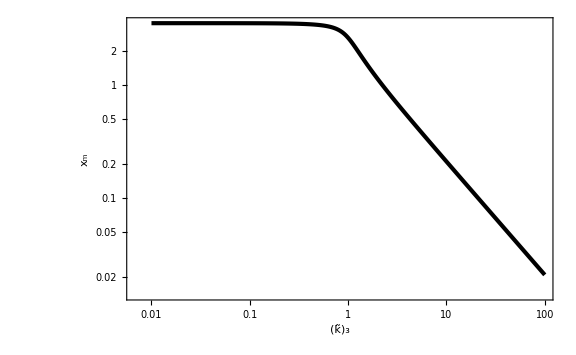

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
Cm[ν2_,k3t_,Ag_]=Simplify[2/3(1-(1+xmint[k3t] σn2[1,s2s]/Sqrt[σn2[2,s2s]] ν2 ζp[xmint[k3t],k3t])^2),{Ag>0,ks>0}];
```

#### Param. search

```mathematica
Cth=533/1000;
As=5 10^-3;(*3.5 10^-3;*)
```

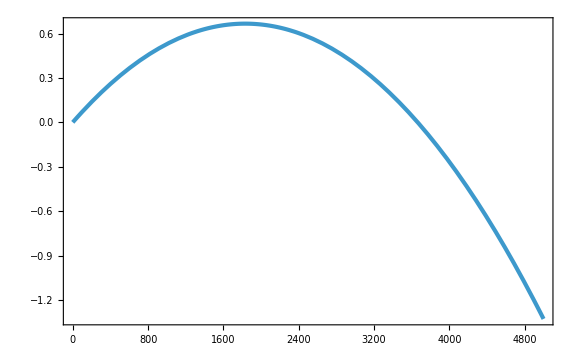

```mathematica
Plot[Cm[nu2,10^1,As],{nu2,0,5000}]
```

```mathematica
k3tc=k3t/.FindRoot[ζx[xmint[k3t],k3t]==0,{k3t,1},WorkingPrecision->30]
```

1.20181939236444583584594606623

```mathematica
padding={{100,10},{70,10}};
```

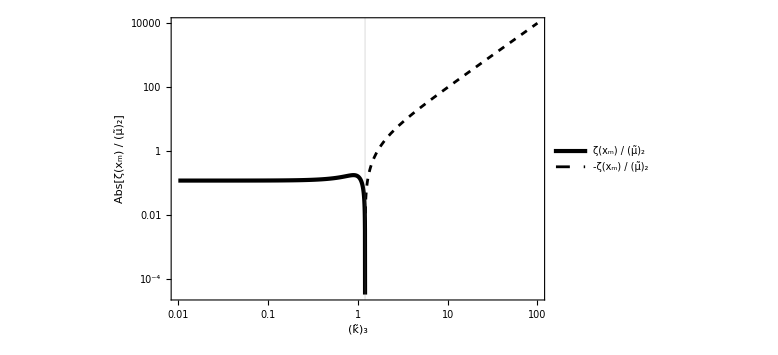

```mathematica
LogLogPlot[{ζx[xmint[k3t],k3t],-ζx[xmint[k3t],k3t]},{k3t,10^-2,10^2},GridLines->{{k3tc},None},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},FrameLabel->{Subscript[OverTilde[k], 3],Abs[Row[{ζ[Subscript[x, "m"]]," / ",Subscript[OverTilde[μ], 2]}]]},PlotLegends->Placed[LineLegend[{Row[{ζ[Subscript[x, "m"]]," / ",Subscript[OverTilde[μ], 2]}],Row[{-ζ[Subscript[x, "m"]]," / ",Subscript[OverTilde[μ], 2]}]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20],{0.8,0.2}],ImagePadding->padding]
```

```mathematica
nu2thList=Table[{10^lnk3t,nu2/.FindRoot[Cm[nu2,10^lnk3t,As]==Cth,{nu2,5},WorkingPrecision->30]},{lnk3t,-2,2,10^-2}];
```

FindRoot::precw: The precision of the argument function (2/3 (1-(1-0.178836242849999753521364739 nu2)^2)==533/1000) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (2/3 (1-(1-0.178835625294999033341342075 nu2)^2)==533/1000) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (2/3 (1-(1-0.178834978635984317321962775 nu2)^2)==533/1000) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

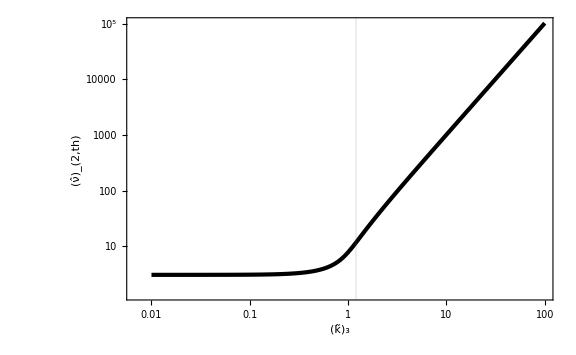

```mathematica
ListLogLogPlot[nu2thList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[OverHat[ν], 2,th]},GridLines->{{k3tc},None},PlotStyle->{Black,AbsoluteThickness[3]},ImagePadding->padding]
```

```mathematica
nu2thint[k3t_]=Interpolation[nu2thList][k3t];
```

```mathematica
MPBH[nu2_,k3t_]=Simplify[xmint[k3t]^2 E^(2 σn2[1,s2s]/Sqrt[σn2[2,s2s]] nu2 ζx[xmint[k3t],k3t])(Cm[nu2,k3t,As]-Cth)^γ/.{γ->36/100,Ag->As(*,Cth->0.533*)},{ks>0}];
dlnMdnu2[nu2_,k3t_]=D[Log[MPBH[nu2,k3t]], nu2];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn[s2s]^2])Exp[-1/2(ν^2+(ξ-γn[s2s] ν)^2/(1-γn[s2s]^2))];
npkPT[nu2_,k3t_,ks_]=Simplify[2/(6π)^(3/2)Sqrt[σn2[4,s2s]/σn2[3,s2s]]^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2],{ks>0}];
```

```mathematica
nu2inMk3tList=Flatten[ParallelTable[{10^lnM,10^lnk3t,nu2thint[10^lnk3t]+10^lndnu2/.FindRoot[MPBH[nu2thint[10^lnk3t]+10^lndnu2,10^lnk3t]==10^lnM,{lndnu2,-2},WorkingPrecision->30]//Quiet},{lnM,-1,1,10^-2},{lnk3t,-2,Log10[k3tc],10^-2}],1];//AbsoluteTiming
```

{121.099,Null}

```mathematica
MPBHmaxList=Table[{10^lnk3t,FindMaximum[MPBH[nu2thint[10^lnk3t]+dnu2,10^lnk3t],{dnu2,1},WorkingPrecision->30][[1]]//Quiet},{lnk3t,-2,Log10[k3tc],10^-2}];
```

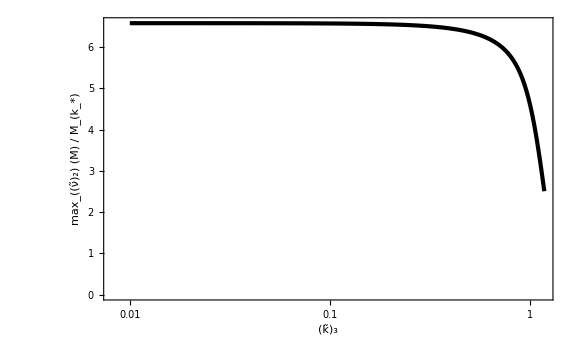

```mathematica
ListLogLinearPlot[MPBHmaxList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Row[{max_Subscript[OverTilde[ν], 2] [M]," / ",Subscript[M, SubStar[k]]}]},PlotStyle->{Black,AbsoluteThickness[3]},ImagePadding->padding]
```

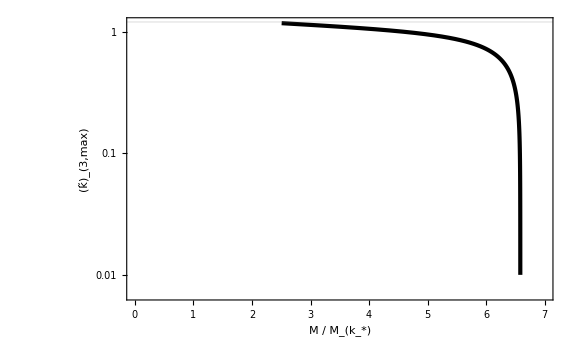

```mathematica
ListLogPlot[RotateRight[MPBHmaxList,{0,1}],PlotRange->{{0,7},Automatic},GridLines->{None,{k3tc}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[OverTilde[k], 3,max]},PlotStyle->{Black,AbsoluteThickness[3]},ImagePadding->padding]
```

```mathematica
Last[MPBHmaxList][[2]]
```

2.50629867531860684827516606191

```mathematica
k3tMint[M_]:=Interpolation[RotateRight[MPBHmaxList,{0,1}]][M]/;M>Last[MPBHmaxList][[2]]
k3tMint[M_]:=k3tc/;M<=Last[MPBHmaxList][[2]]
```

```mathematica
nu2inMk3tList=Flatten[ParallelTable[{10^lnM,10^lnk3t,nu2thint[10^lnk3t]+10^lndnu2/.FindRoot[MPBH[nu2thint[10^lnk3t]+10^lndnu2,10^lnk3t]==10^lnM,{lndnu2,0},WorkingPrecision->30]//Quiet},{lnM,-1,Log10[5],10^-2},{lnk3t,-2,Log10[k3tMint[10^lnM]],10^-2}],1];//AbsoluteTiming
```

{95.3338,Null}

```mathematica
nu2int[M_,k3t_]=Interpolation[nu2inMk3tList][M,k3t];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

```mathematica
Fignu2=ListContourPlot[nu2inMk3tList,PlotRange->{{0,5},{0,1.2},{3.5,12.5}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[OverTilde[k], 3]},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Rotate[Subscript[OverHat[ν], 2],-π/2],Right]]]
```

-Graphics-

```mathematica
Export["../PTISpaper/figs/nu2_LN_0,01.pdf",Fignu2];
```

```mathematica
nPBH[M_]:=NIntegrate[npkPT[nu2int[M,k3t],k3t,kpeak]/Abs[dlnMdnu2[nu2int[M,k3t],k3t]],{k3t,10^-2,k3tMint[M]}]
```

```mathematica
nPBHList=ParallelTable[{10^lnM,nPBH[10^lnM]//Quiet},{lnM,-1,Log10[5],10^-2}];//AbsoluteTiming
```

{296.513,Null}

```mathematica
Export["data/nPBH_LN_0,01_PT2.csv",nPBHList];
```

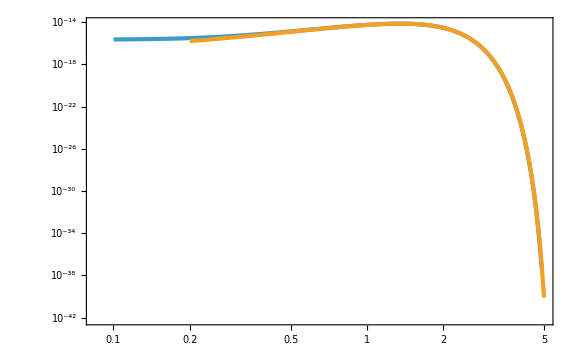

```mathematica
ListLogLogPlot[{nPBHList,Import["data/nPBH_LN_0,01_PT.csv"]}]
```

```mathematica
Mks[ks_]=(NL/L ks/(1.56 10^13))^-2;
```

```mathematica
fPBHList=Map[{#[[1]]Mks[kpeak],#[[1]](#[[2]])/(3.95 10^-20)}&,nPBHList];
Mmin=First[fPBHList][[1]]
Mmax=Last[fPBHList][[1]]
```

0.00240796

0.117937

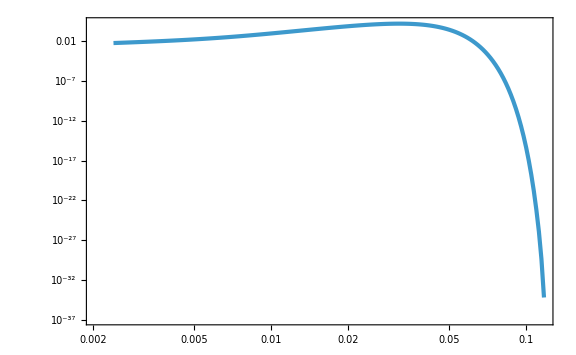

```mathematica
ListLogLogPlot[fPBHList]
```

```mathematica
fPBHint[M_]=Interpolation[fPBHList][M];
```

```mathematica
NIntegrate[fPBHint[M]/M,{M,Mmin,Mmax}]
```

1.39215

```mathematica
Export["data/fPBH_pk_LN_0,01.csv",fPBHList];
```

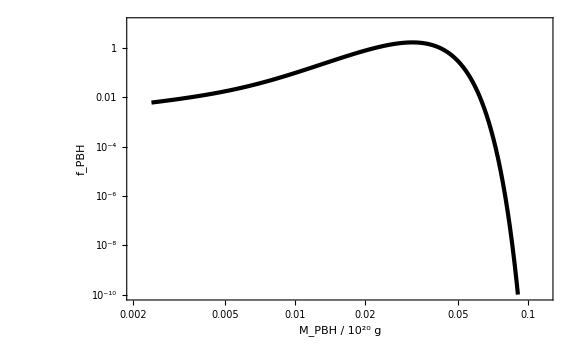

```mathematica
ListLogLogPlot[Import["data/fPBH_pk_LN_0,01.csv"],FrameLabel->{"M_PBH / 10^20 g",Subscript[f, PBH]},PlotStyle->{Black,AbsoluteThickness[3]},PlotRange->{10^-10,10}]
```

## Importance Sampling

```mathematica
npeak=16;
NL=256;
L=10^-12;(*Mpc*)
kpeak=2π npeak/NL;
nbias=16;
```

### Monochromatic

```mathematica
σ2=kpeak^2;
```

```mathematica
Nsim=100;
nu2k3tList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1].DiagonalMatrix[{1/σ2,1/kpeak}];
```

```mathematica
N[Nsim NL^3,2]
```

1.7×10^9

```mathematica
1/Sqrt[2π] E^(-6^2/2)//N
```

6.07588×10^-9

```mathematica
Dnu2=HistogramList[nu2k3tList[[All,1]]][[1,2]]-HistogramList[nu2k3tList[[All,1]]][[1,1]];
nu2min=Mean[HistogramList[nu2k3tList[[All,1]]][[1,1;;2]]];
nnu2IS=Table[{nu2min+Dnu2(i-1),(HistogramList[nu2k3tList[[All,1]]][[2,i]])/(Dnu2 Nsim NL^3)},{i,Length[HistogramList[nu2k3tList[[All,1]]][[2]]]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_,ks_]=ks^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

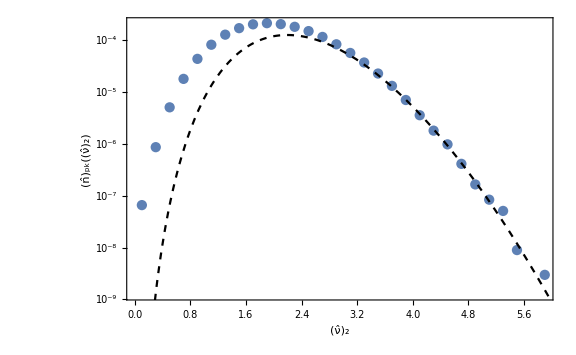

```mathematica
Show[ListLogPlot[nnu2IS,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]}],LogPlot[nnu2PT[nu2,kpeak],{nu2,0,6},PlotStyle->{Dashed,Black}]]
```

```mathematica
ISdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[ISdata]
```

1000

```mathematica
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,ISdata];
```

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"},GridLines->{{0.533},None}]
```

-Graphics-

```mathematica
Dnu2IS=HistogramList[ISdata[[All,2]]/σ2][[1,2]]-HistogramList[ISdata[[All,2]]/σ2][[1,1]]
```

1/2

```mathematica
nu2minIS=HistogramList[ISdata[[All,2]]/σ2][[1,1]]
nu2maxIS=HistogramList[ISdata[[All,2]]/σ2][[1]]//Last
```

5

25/2

```mathematica
nu2binning[nu2_]:=Select[ISdata,nu2<=(#[[2]])/σ2<nu2+Dnu2IS&]
k33sum[mu2_]:=Total[(nu2binning[mu2][[All,3]])^3]
```

```mathematica
nSnu2List=Table[{nu2+Dnu2IS/2,k33sum[nu2]/(Ntot Dnu2IS)},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
```

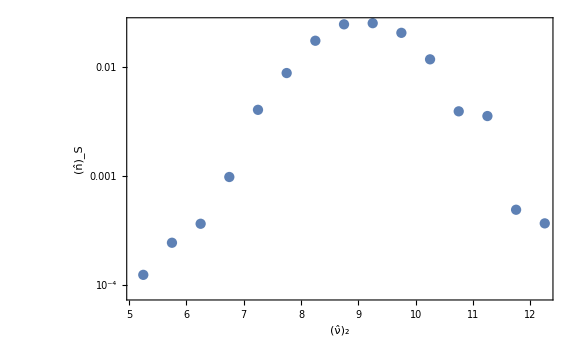

```mathematica
ListLogPlot[nSnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wnu2List=Table[{nu2,If[Length[nu2binning[nu2]]>1,Exp[Mean[nu2binning[nu2][[All,7]]]+Variance[nu2binning[nu2][[All,7]]]/2],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errp=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errm=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[-Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];;
```

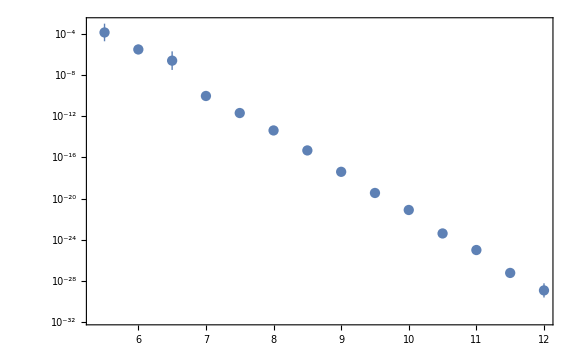

```mathematica
ListLogPlot[Table[{wnu2List[[i,1]],wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[wnu2List]}],Joined->False]
```

```mathematica
nTnu2List=Table[{nSnu2List[[i,1]],nSnu2List[[i,2]]wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[nSnu2List]}];
```

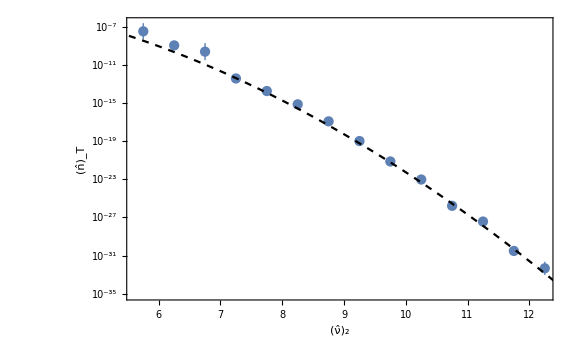

```mathematica
Show[ListLogPlot[nTnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "T"]}],LogPlot[nnu2PT[nu2,kpeak],{nu2,4,15},PlotStyle->{Black,Dashed}]]
```

```mathematica
padding={{100,10},{70,10}};
```

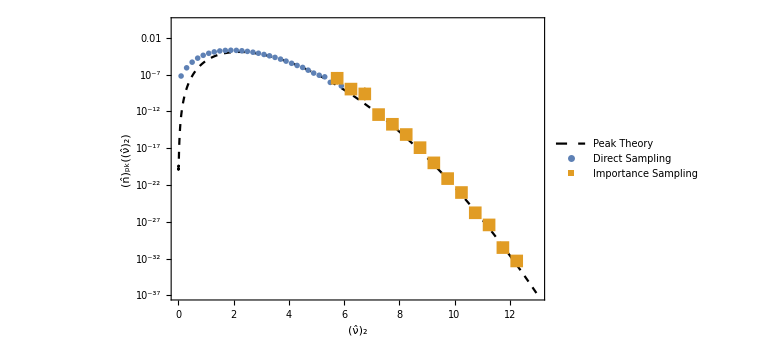

```mathematica
Show[LogPlot[nnu2PT[nu2,kpeak],{nu2,0,13},PlotStyle->{Black,Dashed},FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.3},Right}],ImagePadding->padding],
ListLogPlot[nnu2IS,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.2},Right}]],ListLogPlot[nTnu2List,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.1},Right}]]]
```

```mathematica
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36,Cth->0.533};
```

```mathematica
Mks[ks_]=(NL/L ks/(1.56 10^13))^-2;
```

```mathematica
MPBHList=Map[{#[[3]],MPBH[#[[4]],#[[5]],#[[6]]]Mks[kpeak],#[[7]]}&,Select[ISdata,#[[6]]>0.533&]];
```

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
```

1/10

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last
```

-26/5

-23/10

```mathematica
lnMbinning[lnM_]:=Select[MPBHList,lnM<=Log[#[[2]]]<lnM+DlnM&];
k33sumlnM[lnM_]:=Total[(lnMbinning[lnM][[All,1]])^3]
```

```mathematica
nSlnMList=Table[{lnM+DlnM/2,k33sumlnM[lnM]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];
```

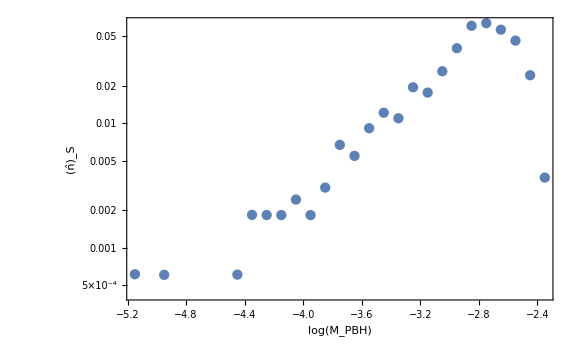

```mathematica
ListLogPlot[nSlnMList,Joined->False,FrameLabel->{Log[Subscript[M, PBH]],Subscript[OverHat[n], "S"]}]
```

```mathematica
wlnMList=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Exp[Mean[lnMbinning[lnM][[All,3]]]+Variance[lnMbinning[lnM][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrp=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrm=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
```

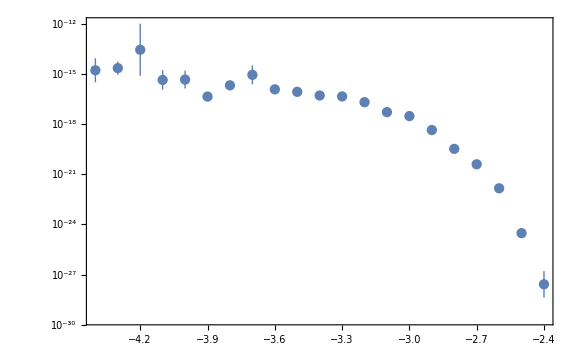

```mathematica
ListLogPlot[Table[{wlnMList[[i,1]],wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[wlnMList]}],Joined->False]
```

```mathematica
nTlnMList=Table[{nSlnMList[[i,1]]//Exp,nSlnMList[[i,2]]wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[nSlnMList]}];
```

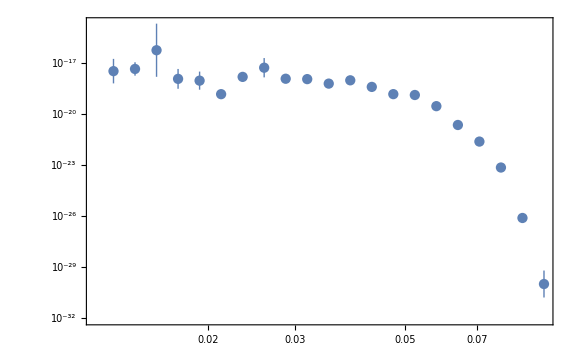

```mathematica
ListLogLogPlot[nTlnMList,Joined->False]
```

```mathematica
fPBHis=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMList];
```

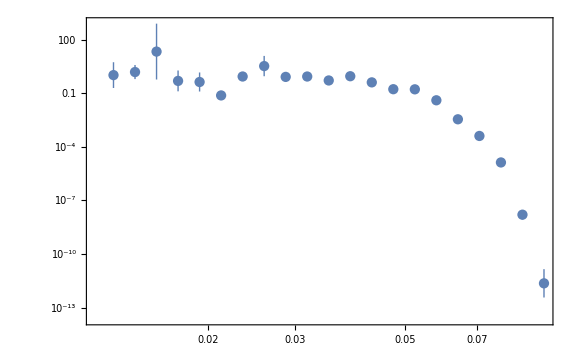

```mathematica
ListLogLogPlot[fPBHis,Joined->False]
```

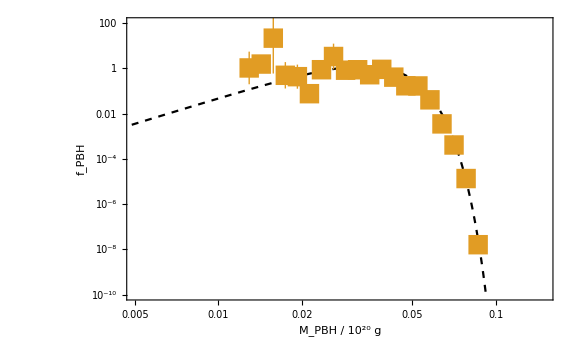

```mathematica
Show[ListLogLogPlot[Import["data/fPBH_pk_mono.csv"],PlotStyle->{Black,Dashed},FrameLabel->{"M_PBH / 10^20 g",Subscript[f, PBH]},PlotRange->{{0.005,0.15},{10^-10,10^2}},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.3}],ImagePadding->padding],
ListLogLogPlot[fPBHis,Joined->False,PlotMarkers->Style["■",Color[2],20],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.3}]]]
```

### Sharp lognormal

```mathematica
s2=0.01;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
```

```mathematica
Nsim=10;
nu2k3tList=Flatten[Table[Import["data/LN_peak_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1].DiagonalMatrix[{1/σ2,1/kpeak}];
```

```mathematica
Dnu2=HistogramList[nu2k3tList[[All,1]]][[1,2]]-HistogramList[nu2k3tList[[All,1]]][[1,1]];
nu2min=Mean[HistogramList[nu2k3tList[[All,1]]][[1,1;;2]]];
nnu2IS=Table[{nu2min+Dnu2(i-1),(HistogramList[nu2k3tList[[All,1]]][[2,i]])/(Dnu2 Nsim NL^3)},{i,Length[HistogramList[nu2k3tList[[All,1]]][[2]]]}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

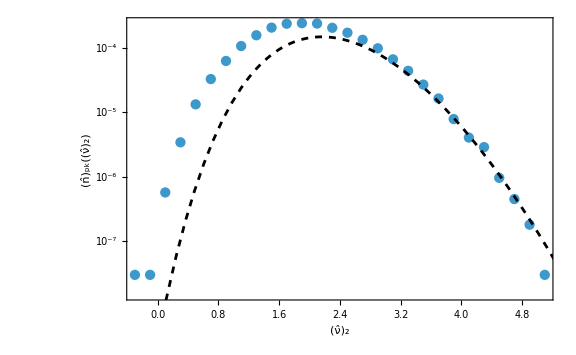

```mathematica
Show[ListLogPlot[nnu2IS,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]}],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black}]]
```

```mathematica
ISdata=Import["data/LN_muk_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_GB.csv"];
Ntot=Length[ISdata]
```

161

```mathematica
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,ISdata];
```

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"},GridLines->{{0.533},None}]
```

-Graphics-

```mathematica
Dnu2IS=HistogramList[ISdata[[All,2]]/σ2][[1,2]]-HistogramList[ISdata[[All,2]]/σ2][[1,1]]
```

1/2

```mathematica
nu2minIS=HistogramList[ISdata[[All,2]]/σ2][[1,1]]
nu2maxIS=HistogramList[ISdata[[All,2]]/σ2][[1]]//Last
```

11/2

11

```mathematica
nu2binning[nu2_]:=Select[ISdata,nu2<=(#[[2]])/σ2<nu2+Dnu2IS&]
k33sum[mu2_]:=Total[(nu2binning[mu2][[All,3]])^3]
```

```mathematica
nSnu2List=Table[{nu2+Dnu2IS/2,k33sum[nu2]/(Ntot Dnu2IS)},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
```

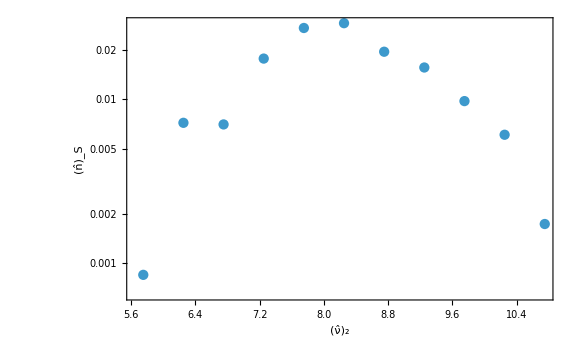

```mathematica
ListLogPlot[nSnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wnu2List=Table[{nu2,If[Length[nu2binning[nu2]]>1,Exp[Mean[nu2binning[nu2][[All,7]]]+Variance[nu2binning[nu2][[All,7]]]/2],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errp=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errm=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[-Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];;
```

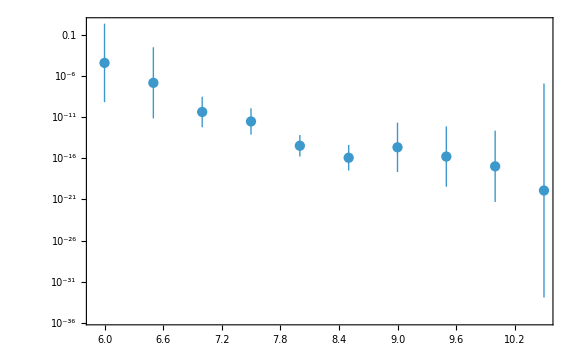

```mathematica
ListLogPlot[Table[{wnu2List[[i,1]],wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[wnu2List]}],Joined->False]
```

```mathematica
nTnu2List=Table[{nSnu2List[[i,1]],nSnu2List[[i,2]]wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[nSnu2List]}];
```

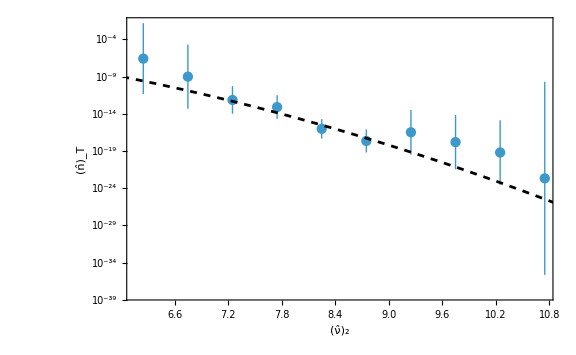

```mathematica
Show[ListLogPlot[nTnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "T"]}],LogPlot[nnu2PT[nu2],{nu2,4,15},PlotStyle->{Black,Dashed}]]
```

```mathematica
padding={{100,10},{70,10}};
```

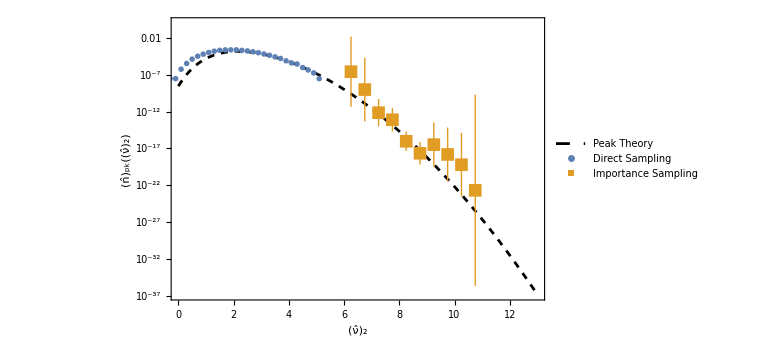

```mathematica
Show[LogPlot[nnu2PT[nu2],{nu2,0,13},PlotStyle->{Black,Dashed},FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.3},Right}],ImagePadding->padding],
ListLogPlot[nnu2IS,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.2},Right}]],ListLogPlot[nTnu2List,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.1},Right}]]]
```

```mathematica
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36,Cth->0.533};
```

```mathematica
Mks[ks_]=(NL/L ks/(1.56 10^13))^-2;
```

```mathematica
MPBHList=Map[{#[[3]],MPBH[#[[4]],#[[5]],#[[6]]]Mks[kpeak],#[[7]]}&,Select[ISdata,#[[6]]>0.533&]];
```

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
```

1/2

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last
```

-5

-5/2

```mathematica
lnMbinning[lnM_]:=Select[MPBHList,lnM<=Log[#[[2]]]<lnM+DlnM&];
k33sumlnM[lnM_]:=Total[(lnMbinning[lnM][[All,1]])^3]
```

```mathematica
nSlnMList=Table[{lnM+DlnM/2,k33sumlnM[lnM]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];
```

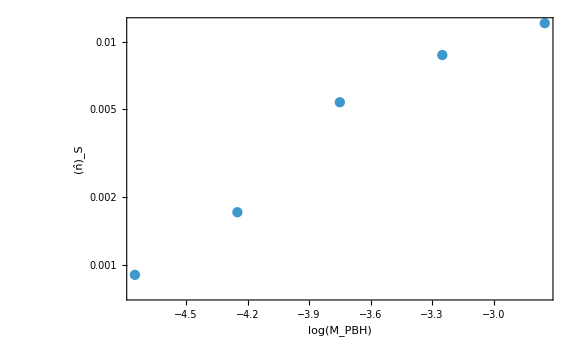

```mathematica
ListLogPlot[nSlnMList,Joined->False,FrameLabel->{Log[Subscript[M, PBH]],Subscript[OverHat[n], "S"]}]
```

```mathematica
wlnMList=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Exp[Mean[lnMbinning[lnM][[All,3]]]+Variance[lnMbinning[lnM][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrp=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrm=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
```

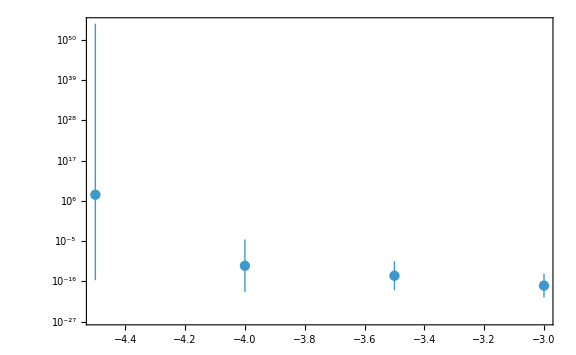

```mathematica
ListLogPlot[Table[{wlnMList[[i,1]],wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[wlnMList]}],Joined->False]
```

```mathematica
nTlnMList=Table[{nSlnMList[[i,1]]//Exp,nSlnMList[[i,2]]wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[nSlnMList]}];
```

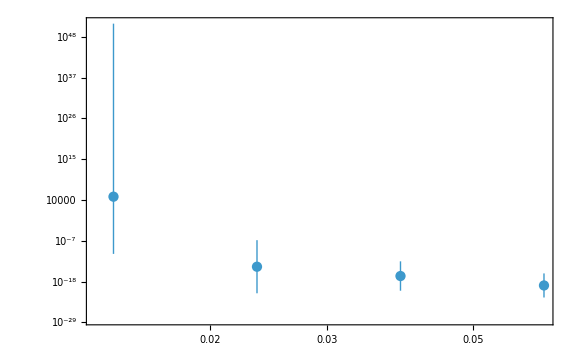

```mathematica
ListLogLogPlot[nTlnMList,Joined->False]
```

```mathematica
fPBHis=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMList];
```

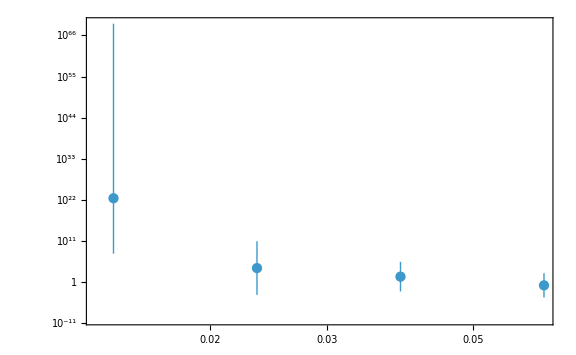

```mathematica
ListLogLogPlot[fPBHis,Joined->False]
```

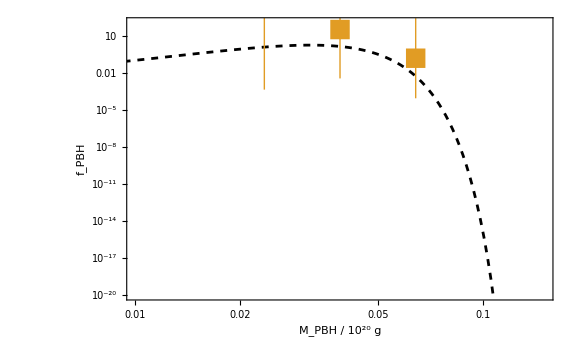

```mathematica
Show[ListLogLogPlot[Import["data/fPBH_pk_LN_0,01.csv"],PlotStyle->{Black,Dashed},FrameLabel->{"M_PBH / 10^20 g",Subscript[f, PBH]},PlotRange->{{0.01,0.15},{10^-20,10^2}},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.3}],ImagePadding->padding],
ListLogLogPlot[fPBHis,Joined->False,PlotMarkers->Style["■",Color[2],20],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.3}]]]
```